# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 3 - The Finite Difference Method: Tunneling

## 3.2 EXAMPLE: SQUARE BARRIER

### 3.2.1 Defining the potential

```mathematica
V0=9;(*barrier height in a.u.*)
V[x_]:=Piecewise[{
{0,x<4},
{V0,4≤x≤5},(*only nonzero between 4a0 and 5a0*)
{0,x>5}}];
```

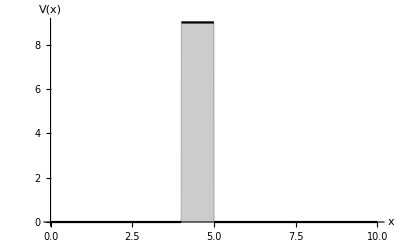

```mathematica
Plot[V[x],{x,0,10},Filling->Axis,AxesLabel->{"x","V(x)"}]
```

### 3.2.2 Implementation of the finite difference scheme

```mathematica
hbar=1; (*define variables in atomic units*)
m=1; (*incoming particle mass = 1 Subscript[m, e]*)
a=0.01; (*spacing between simulation grid points in Subscript[a, 0]*)
xTotal=10; (*total length of simulation box in Subscript[a, 0]*)
nPoints=xTotal/a; (*number of points on the simulation grid*)
energy=9; (*kinetic energy of incoming particle*)
k=Sqrt[2*m*energy/hbar^2];(*plane wave parameter*)
xcoords=Table[N[a*j],{j,1,nPoints}]; (*x-axis*)
```

```mathematica
psi=Table[0,{j,1,nPoints}];(*initialize wavefunction table*)
psi[[1]]=N[Exp[-I*k*a]];(*first point*)
psi[[2]]=(*second point*)N[(2+2*m*(V[xcoords[[2]]]-energy)*a^2/hbar^2)*psi[[1]]-1];
Do[ (*subsequent points;uses recursive definition*)
psi[[j+1]]=N[(2+2*m*(V[xcoords[[j]]]-energy)*a^2/hbar^2)*psi[[j]]-psi[[j-1]]],{j,2,nPoints-1}];
psiSquared=Re[Conjugate[psi]*psi];
```

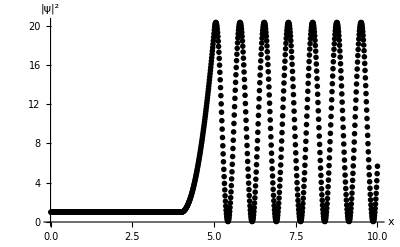

```mathematica
ListPlot[Table[{xcoords[[j]],psiSquared[[j]]},{j,1,nPoints}],AxesLabel->{"x","|ψ|^2"}]
```

### 3.2.3 Computing transmission versus incident kinetic energy

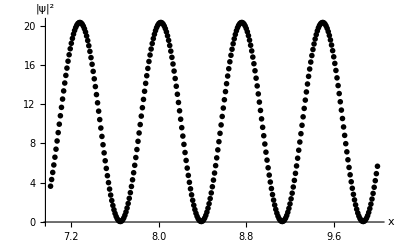

```mathematica
ListPlot[
Partition[Riffle[xcoords,psiSquared],2][[-300;;-1]],
AxesLabel->{"x","|ψ|^2"}]
```

```mathematica
PMin=Min[psiSquared[[-300;;-1]]]
PMax=Max[psiSquared[[-300;;-1]]]
```

0.0494314

20.3196

```mathematica
trans=2/(1+(PMin+PMax)/2)
```

0.178819

```mathematica
transmission[energy_]:=Module[{k,psi,psiSquared},
k=Sqrt[2*m*energy/hbar^2];(*define k for current energy*)
psi=Table[0,{j,1,nPoints}];(*compute ψ as before*)
psi[[1]]=N[Exp[-I*k*a]];psi[[2]]=N[(2+2*m*(V[xcoords[[2]]]-energy)*a^2/hbar^2)*psi[[1]]-1];Do[psi[[j+1]]=N[(2+2*m*(V[xcoords[[j]]]-energy)*a^2/hbar^2)*psi[[j]]-psi[[j-1]]],{j,2,nPoints-1}];
psiSquared=Re[Conjugate[psi]*psi];
(*return the transmission probability*)2/(1+(Min[psiSquared[[-300;;-1]]]+Max[psiSquared[[-300;;-1]]])/2)
];
```

```mathematica
transmission[9]
```

0.178819

```mathematica
hbar=1;m=1;a=0.01;xTotal=10;nPoints=xTotal/a;
V0=9; (*define variables as before*)

squareBarrierTransmissionData=Table[
{energy,transmission[energy]},{energy,1,26,0.1}];
```

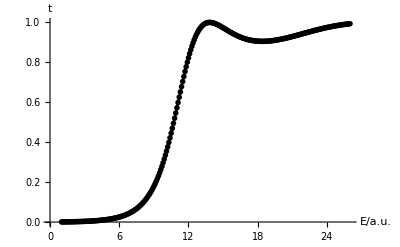

```mathematica
ListPlot[squareBarrierTransmissionData,
Joined->True,AxesOrigin->{0,0},AxesLabel->{"E/a.u.","t"}]
```

## 3.3 GAUSSIAN BARRIER

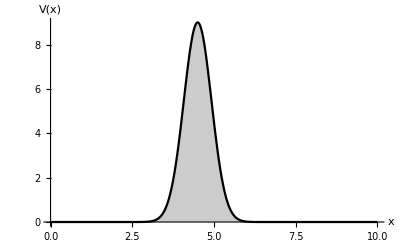

```mathematica
A=9;X=4.5;c=0.6;(*Gaussian barrier parameters,in a.u.*)
V[x_]:=A*Exp[-((x-X)/c)^2];
Plot[ V[x],{x,0,xTotal},
Filling->Axis,AxesLabel->{"x","V(x)"},PlotRange->All]
```

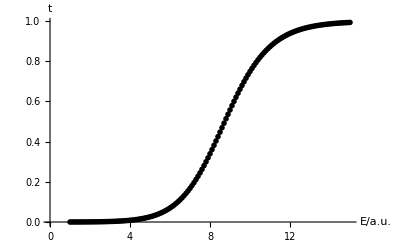

```mathematica
hbar=1;m=1;a=0.01;xTotal=10;nPoints=xTotal/a;

gaussianTransmissionData=Table[
{energy,transmission[energy]},{energy,1,15,0.1}];

ListPlot[gaussianTransmissionData,
Joined->True,AxesLabel->{"E/a.u.","t"}]
```